### Globals

```mathematica
$HistoryLength=0;ClearAll["Global`*"];
```

```mathematica
au=1.5*10^13;
G=6.67*10^-8;
σ = 5.67*10^-5;
Msun=2*10^33;
year=3.15*10^7;
Rsun=0.00465 au; 
days = 24*60*60;
```

### Params

```mathematica
sizeFactor=1.0;
Bstar = 1000;
Tstar =5777;
Mstar=sizeFactor*Msun;
Rstar = sizeFactor*2 * Rsun;
mdot = sizeFactor * 10^-8 Msun/year;
Pstar = 7 days;
```

### Truncation Radius

```mathematica
rmsAu=((3 Bstar^2 Rstar^6)/(2 mdot √(G Mstar)))^(2/7)/au
```

0.0749608

```mathematica
rcoAu=((G Mstar Pstar^2)/(4 π^2))^(1/3)/au
```

0.0715454

### Active Disk Temperature Model

```mathematica
TdiskActive[r_]:=((3 G Mstar mdot)/(8 π σ (r*au)^3)(1-√(Rstar/(r*au))))^(1/4)
diskMassFraction=0.024033;
kr=3;
Σ[r_]:=(diskMassFraction/0.024033*Mstar/Msun)1700* (r)^(-3/2);
```

```mathematica
τ[r_]:=1/2 Σ[r]* kr
TcActive[r_]:=(TdiskActive[r]^4 3/4 τ[r])^(1/4)
```

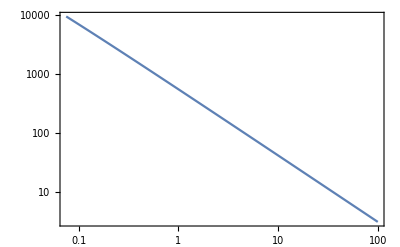

```mathematica
LogLogPlot[TcActive[r],{r,rmsAu,100}, Frame->True,GridLines->{{},{1000}}]
```

```mathematica
Solve[TcActive[r]==1000,r,Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→0.0093},{r→0.583108}}